```mathematica
CartesianMap::usage="Plots the image of the cartesian coordinate lines under the function f.
Example:
CartesianMap[Sin,{x,-2,2},{y,-2,2},Mesh→60]
CartesianMap[Exp[-#^2]*Erfc[-I*#]&,{x,0,4},{y,0,4},Mesh→60]
";
CartesianMap[f_,opts___]:= ParametricPlot[{Re[f[x+I*y]], Im[f[x+I*y]]},opts];

CartesianConformal::usage = "Plots conformal mapping"
CartesianConformal[func_,xrange_,yrange_,opts___]:=
{CartesianMap[#&,xrange,yrange,opts,DisplayFunction->Identity],
CartesianMap[func,xrange,yrange,opts,DisplayFunction->Identity]}
```

Plots conformal mapping

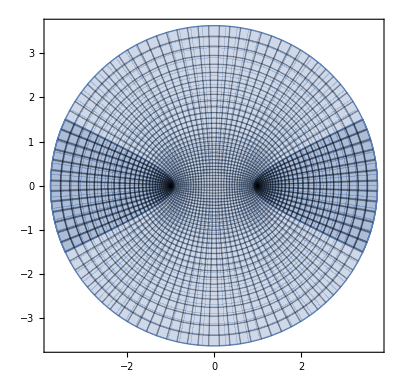

```mathematica
CartesianMap[Sin,{x,-2,2},{y,-2,2},Mesh->60]
```

```mathematica
?CartesianMap
```

Plots the image of the cartesian coordinate lines under the function f.
Example:
CartesianMap[Sin,{x,-2,2},{y,-2,2},Mesh→60]
CartesianMap[Exp[-#^2]*Erfc[-I*#]&,{x,0,4},{y,0,4},Mesh→60]

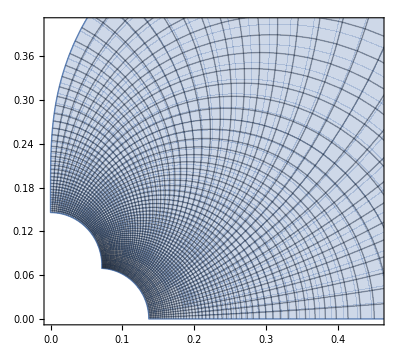

```mathematica
CartesianMap[Exp[-#^2]*Erfc[-I*#]&,{x,0,4},{y,0,4},Mesh->60]
```

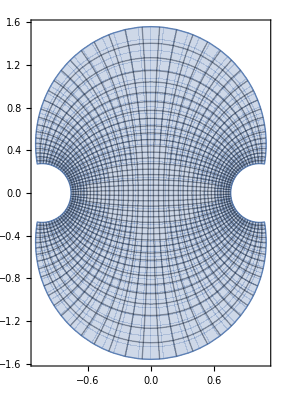

```mathematica
CartesianMap[Tanh,{x,-1,1},{y,-1,1},Mesh->40]
```

```mathematica
CartesianConformal[func_,xrange_,yrange_,opts___]:=
{CartesianMap[#&,xrange,yrange,opts,DisplayFunction->Identity],
CartesianMap[func,xrange,yrange,opts,DisplayFunction->Identity]}
```

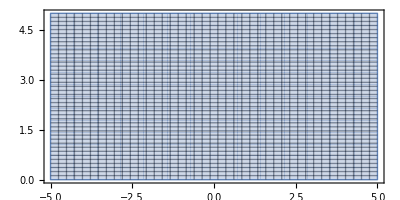
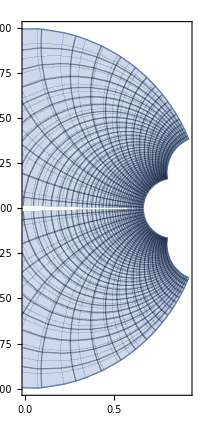

```mathematica
CartesianConformal[((#-I)/(#+I))&,{x,-5,5},{y,0,5},Mesh->40]
```

```mathematica
?CartesianConformal
```

Plots conformal mapping

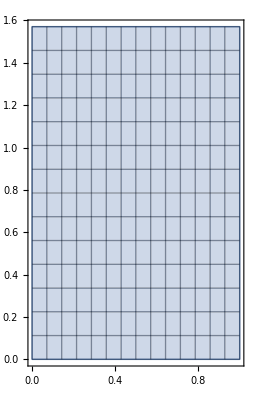
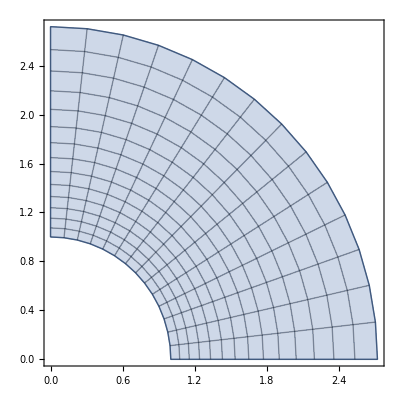

```mathematica
CartesianConformal[Exp,{x,0,1},{y,0,Pi/2},PlotRange->All,Mesh->Full]
```